```mathematica
ChebyshevT[1, x]+ChebyshevT[3, x]+ChebyshevT[5, x]+ChebyshevT[7, x]
```

-4 x+40 x^3-96 x^5+64 x^7

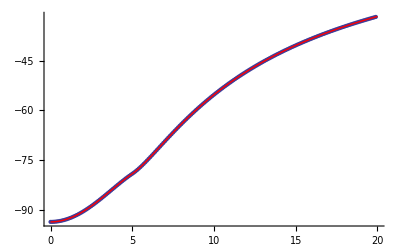

```mathematica
R=5;
fin[r_]:=(R*r^2)/6-r^4/(20R)-(3 R^3)/4;
fout[r_]:=R^5/(2 r^2)-(17 R^4)/(15r);
phidata=Import["fofr.txt", "Data"];
plot1=ListPlot[phidata];
rmax=phidata⟦-1,1⟧;
plot2=Plot[fin[r], {r, 0, R}, PlotRange->{{0, rmax},{-100, 0}}, PlotStyle->Red];
plot3=Plot[fout[r], {r, R, 20}, PlotRange->{{0, rmax},{-100, 0}}, PlotStyle->Red];
Show[plot1, plot2, plot3]
```

```mathematica
α=-1/(2R);
r[x_]:=1/(α(x-1));
```

```mathematica
Expand[fout[r[x]]]
```

-53/120+(19 x)/60+x^2/8

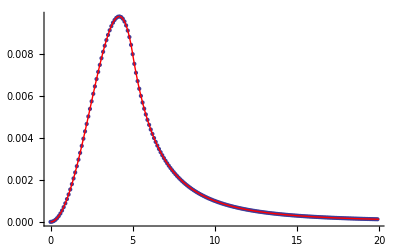

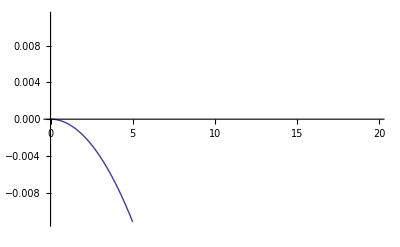

```mathematica
R=5;
L=2;
fin[r_]:=(L+5)r^2/(2 R^(L+3))-(L+3)r^4/(2 R^(L+5));
fout[r_]:=1/r^(L+1);
sourcein[r_]:=1/2(L+3)(L+5)(((L-4)r^2)/R^(L+5)-(L-2)/R^(L+3))
phidata=Import["fofr.txt", "Data"];
rmax=phidata⟦-1,1⟧;
phimin=Min[phidata⟦All, 2⟧];
phimax=Max[phidata⟦All, 2⟧];
plot1=ListPlot[phidata, PlotRange->{{0, rmax},{phimin, phimax}}];
plot2=Plot[fin[r], {r, 0, R}, PlotRange->{{0, rmax},{phimin, phimax}}, PlotStyle->Red];
plot3=Plot[fout[r], {r, R, 20}, PlotRange->{{0, rmax},{phimin, phimax}}, PlotStyle->Red];
Show[plot1, plot2, plot3]
Plot[sourcein[r], {r, 0, R}, PlotRange->{{0, rmax},{-Abs[sourcein[R]], Abs[sourcein[R]]}}]
```

```mathematica
N[sourcein[0]]
```

0.

```mathematica
N[fin[R]]
N[fout[R]]
N[fin'[R]]
N[fout'[R]]
```

0.00032

0.00032

-0.00032

-0.00032

```mathematica
fin[r_]:=(L+5)r^2/(2 R^(L+3))-(L+3)r^4/(2 R^(L+5));
```

```mathematica
Simplify[fin''[r]+2/r fin'[r]-(L(L+1))/r^2 fin[r]]
```

1/2 (15+8 L+L^2) R^(-5-L) ((-4+L) r^2-(-2+L) R^2)

```mathematica
Solve[{1/R^(L+1)==A*R^2+B*R^4,(-(L+1))/R^(L+2)==2A*R+4B*R^3}, {A, B}]
```

{{A→1/2 (5+L) R^(-3-L),B→-1/2 (3+L) R^(-5-L)}}

```mathematica
Plot3D[sourcein[(x^2+y^2)^(1/2)]*SphericalHarmonicY[L, 0, , {x, -10, 10}, {y, -10, 10}, RegionFunction->Function[{x,y,z},x^2+y^2<R^2]]
```

-Graphics3D-

```mathematica
Plot3D[sourcein[r]*SphericalHarmonicY[L, 0, θ, 2], {r, 0, R}, {θ, 0, 2π}]
```

-Graphics3D-

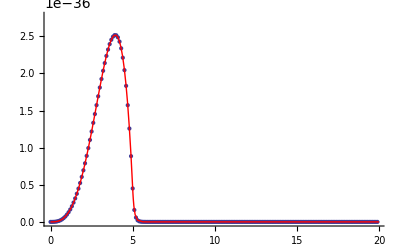

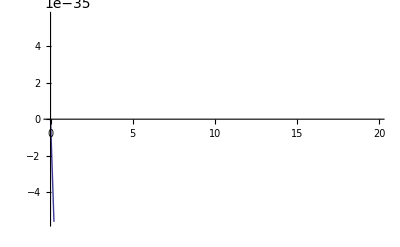

```mathematica
R=5;
L=51;
fin[r_]:=(L+6)r^3/(2 R^(L+4))-(L+4)r^5/(2 R^(L+6));
fout[r_]:=1/r^(L+1);
sourcein[r_]:=1/2(L+4)(L+6)(-((L-3)r)/R^(L+4)+((L-5)r^3)/R^(L+6));
phidata=Import["fofr.txt", "Data"];
rmax=phidata⟦-1,1⟧;
phimin=Min[phidata⟦All, 2⟧];
phimax=1.1*Max[phidata⟦All, 2⟧];
plot1=ListPlot[phidata, PlotRange->{{0, rmax},{phimin, phimax}}];
plot2=Plot[fin[r], {r, 0, R}, PlotRange->{{0, rmax},{phimin, phimax}}, PlotStyle->Red];
plot3=Plot[fout[r], {r, R, 20}, PlotRange->{{0, rmax},{phimin, phimax}}, PlotStyle->Red];
Show[plot1, plot2, plot3]
Plot[sourcein[r], {r, 0, R}, PlotRange->{{0, rmax},{-Abs[sourcein[R]], Abs[sourcein[R]]}}]
```

```mathematica
N[fin[R]]
N[fout[R]]
N[fin'[R]]
N[fout'[R]]
```

0.04

0.04

-0.016

-0.016

```mathematica
L=1;
s[x_]:=-7/250 ChebyshevT[1, x]-7/250 ChebyshevT[3, x]
f[x_]:=-7/180 ChebyshevT[3, x]-7/720 ChebyshevT[5, x]
```

```mathematica
Expand[s[x]]
Expand[f''[x]+2/x f'[x]-(L(L+1))/x^2 f[x]]
```

(7 x)/125-(14 x^3)/125

(7 x)/18-(196 x^3)/45

```mathematica
A={{80, 60, 352},{32, 288, 400},{0, 120, 480}};
S={-189/2500, -63/2500, 0};
F=LinearSolve[A,S]
```

{-777/830000,21/830000,-21/3320000}